```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
v2mColor=Purple;
```

```mathematica
(***************************)
```

```mathematica
dateMouseSessionListV2m={{"011721","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"010321","Mouse23382","Session1"},{"010621","Mouse23382","Session2"},{"111420","Mouse23383","Session3"},{"111720","Mouse23383","Session1"},{"112120","Mouse23383","Session2"},{"120520","Mouse23383","Session2"},{"092620","Mouse21069","Session2"},{"093020","Mouse21069","Session2"},{"092020","Mouse21011","Session2"},{"090420","Mouse21076","Session1"},{"090520","Mouse21076","Session2"},{"022821","Mouse23390","Session1"},{"030421","Mouse23390","Session1"},{"021721","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"021821","Mouse23310","Session1"},{"022621","Mouse23310","Session2"},{"030221","Mouse23310","Session1"},{"031121","Mouse23310","Session1"},{"031921","Mouse23310","Session2"}};
```

```mathematica
dateMouseSessionListV1toV2m={{"082120","Mouse21060","Session2"},{"082320","Mouse21060","Session2"},{"090820","Mouse21067","Session2"},{"121820","Mouse23365","Session1"},{"122020","Mouse23365","Session1"},{"121020","Mouse23379","Session1"},{"121820","Mouse23379","Session1"},{"121920","Mouse23379","Session1"},{"101620","Mouse23392","Session2"},{"101820","Mouse23392","Session3"},{"102520","Mouse23392","Session1"},{"101620","Mouse23393","Session1"},{"101520","Mouse23395","Session2"},{"020421","Mouse23320","Session1"},{"020421","Mouse23329","Session1"},{"021321","Mouse23329","Session1"},{"030121","Mouse23329","Session1"},{"030621","Mouse23329","Session1"},{"080221","Mouse21108","Session1"},{"062522","Mouse23007","Session1"},{"062922","Mouse23007","Session1"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"092421","Mouse22422","Session1"},{"081621","Mouse22437","Session1"},{"081921","Mouse22437","Session1"},{"082821","Mouse22437","Session1"},{"082021","Mouse22491","Session1"},{"102221","Mouse22422","Session1"},{"101821","Mouse22436","Session1"},{"102021","Mouse22472","Session1"},{"102821","Mouse22472","Session2"},{"102921","Mouse22436","Session1"},{"071522","Mouse23025","Session1"},{"072022","Mouse23025","Session1"},{"071222","Mouse23100","Session1"},{"071522","Mouse23100","Session1"},{"070922","Mouse23014","Session1"},{"071422","Mouse23014","Session1"},{"070822","Mouse22518","Session1"},{"071122","Mouse22518","Session1"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"102920","Mouse23377","Session2"},{"110120","Mouse23377","Session1"},{"110220","Mouse23377","Session2"},{"103120","Mouse23378","Session2"},{"120420","Mouse23378","Session1"},{"120220","Mouse23378","Session2"},{"121620","Mouse23381","Session2"},{"121920","Mouse23381","Session1"},{"111720","Mouse23384","Session3"},{"112020","Mouse23384","Session2"},{"120420","Mouse23384","Session1"},{"102020","Mouse23394","Session2"},{"102220","Mouse23394","Session3"},{"102920","Mouse23394","Session2"},{"100720","Mouse23399","Session2"},{"102320","Mouse23399","Session1"},{"010721","Mouse23339","Session1"},{"010821","Mouse23339","Session1"},{"011421","Mouse23339","Session2"},{"011221","Mouse23369","Session1"},{"011521","Mouse23369","Session1"},{"070122","Mouse23067","Session1"},{"063022","Mouse23075","Session1"},{"070822","Mouse23075","Session2"}};
```

```mathematica
(***************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3B****************) 
(**********************************************)
```

```mathematica
meanDFFzOnsetV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/meanDFFzTraceOnset_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOnsetV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/semDFFzTraceOnset_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOffsetV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/meanDFFzTraceOffset_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOffsetV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/semDFFzTraceOffset_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOnsetLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/meanDFFzTraceOnset_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOnsetLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/semDFFzTraceOnset_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOffsetLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/meanDFFzTraceOffset_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOffsetLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/semDFFzTraceOffset_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOnsetLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/meanDFFzTraceOnset_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOnsetLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/semDFFzTraceOnset_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOffsetLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/meanDFFzTraceOffset_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFzOffsetLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/semDFFzTraceOffset_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFzOnsetV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/meanDFFzTraceOnset_V2m.txt","List"];
```

```mathematica
semDFFzOnsetV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/semDFFzTraceOnset_V2m.txt","List"];
```

```mathematica
meanDFFzOffsetV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/meanDFFzTraceOffset_V2m.txt","List"];
```

```mathematica
semDFFzOffsetV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/semDFFzTraceOffset_V2m.txt","List"];
```

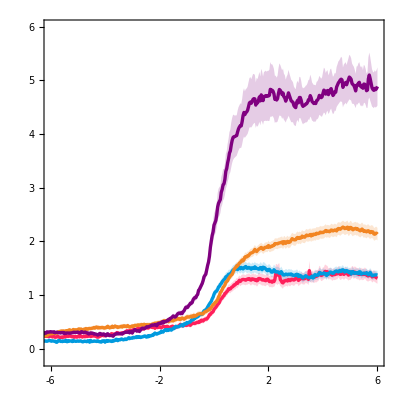

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOnsetV1toV2m,Part[#,2]&/@meanDFFzOnsetV1toV2m+(Part[#,2]&/@semDFFzOnsetV1toV2m),Part[#,2]&/@meanDFFzOnsetV1toV2m-(Part[#,2]&/@semDFFzOnsetV1toV2m),Part[#,2]&/@meanDFFzOnsetLPtoV2m,Part[#,2]&/@meanDFFzOnsetLPtoV2m+(Part[#,2]&/@semDFFzOnsetLPtoV2m),Part[#,2]&/@meanDFFzOnsetLPtoV2m-(Part[#,2]&/@semDFFzOnsetLPtoV2m),Part[#,2]&/@meanDFFzOnsetLMtoV2m,Part[#,2]&/@meanDFFzOnsetLMtoV2m+(Part[#,2]&/@semDFFzOnsetLMtoV2m),Part[#,2]&/@meanDFFzOnsetLMtoV2m-(Part[#,2]&/@semDFFzOnsetLMtoV2m),Part[#,2]&/@meanDFFzOnsetV2m,Part[#,2]&/@meanDFFzOnsetV2m+(Part[#,2]&/@semDFFzOnsetV2m),Part[#,2]&/@meanDFFzOnsetV2m-(Part[#,2]&/@semDFFzOnsetV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-15,6},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-6,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

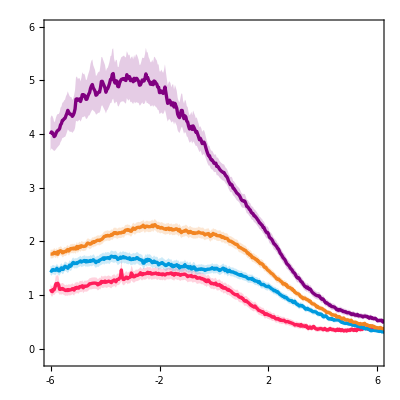

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOffsetV1toV2m,Part[#,2]&/@meanDFFzOffsetV1toV2m+(Part[#,2]&/@semDFFzOffsetV1toV2m),Part[#,2]&/@meanDFFzOffsetV1toV2m-(Part[#,2]&/@semDFFzOffsetV1toV2m),Part[#,2]&/@meanDFFzOffsetLPtoV2m,Part[#,2]&/@meanDFFzOffsetLPtoV2m+(Part[#,2]&/@semDFFzOffsetLPtoV2m),Part[#,2]&/@meanDFFzOffsetLPtoV2m-(Part[#,2]&/@semDFFzOffsetLPtoV2m),Part[#,2]&/@meanDFFzOffsetLMtoV2m,Part[#,2]&/@meanDFFzOffsetLMtoV2m+(Part[#,2]&/@semDFFzOffsetLMtoV2m),Part[#,2]&/@meanDFFzOffsetLMtoV2m-(Part[#,2]&/@semDFFzOffsetLMtoV2m),Part[#,2]&/@meanDFFzOffsetV2m,Part[#,2]&/@meanDFFzOffsetV2m+(Part[#,2]&/@semDFFzOffsetV2m),Part[#,2]&/@meanDFFzOffsetV2m-(Part[#,2]&/@semDFFzOffsetV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-6,15},PlotRange->{{-6,6},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-6,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

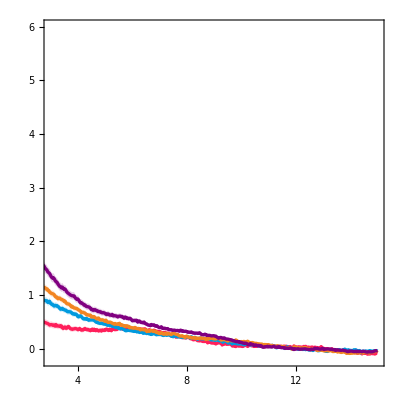

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFzOffsetV1toV2m,Part[#,2]&/@meanDFFzOffsetV1toV2m+(Part[#,2]&/@semDFFzOffsetV1toV2m),Part[#,2]&/@meanDFFzOffsetV1toV2m-(Part[#,2]&/@semDFFzOffsetV1toV2m),Part[#,2]&/@meanDFFzOffsetLPtoV2m,Part[#,2]&/@meanDFFzOffsetLPtoV2m+(Part[#,2]&/@semDFFzOffsetLPtoV2m),Part[#,2]&/@meanDFFzOffsetLPtoV2m-(Part[#,2]&/@semDFFzOffsetLPtoV2m),Part[#,2]&/@meanDFFzOffsetLMtoV2m,Part[#,2]&/@meanDFFzOffsetLMtoV2m+(Part[#,2]&/@semDFFzOffsetLMtoV2m),Part[#,2]&/@meanDFFzOffsetLMtoV2m-(Part[#,2]&/@semDFFzOffsetLMtoV2m),Part[#,2]&/@meanDFFzOffsetV2m,Part[#,2]&/@meanDFFzOffsetV2m+(Part[#,2]&/@semDFFzOffsetV2m),Part[#,2]&/@meanDFFzOffsetV2m-(Part[#,2]&/@semDFFzOffsetV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-6,15},PlotRange->{{3,15},{-0.2,6}},FrameTicks->{{LinTicks[-0.2,6,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[3,15,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3C****************) 
(**********************************************)
```

```mathematica
(***Import overall loc mod values***)
```

```mathematica
locModValsV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/locModIndexSummVals_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
locModValsLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/locModIndexSummVals_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
locModValsLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/locModIndexSummVals_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
locModValsV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/locModIndexSummVals_V2m.txt","List"];
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[locModValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[locModValsV1toV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[locModValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[locModValsLMtoV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[locModValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[locModValsLPtoV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v2mAxonCharts=Show[BoxWhiskerChart[locModValsV2m,{{"Whiskers", Directive[Darker@v2mColor,Thick]}, {"Fences", Directive[Darker@v2mColor,Thick]},{"MedianMarker", Directive[Darker@v2mColor,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Directive[v2mColor,Opacity[0.3]],Frame->False],DistributionChart[locModValsV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v2mColor],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[locModValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-1.2,1}},ChartStyle->Transparent,Frame->False],DistributionChart[locModValsV2m,PlotRange->{All,{-1.2,1}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-1.2,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

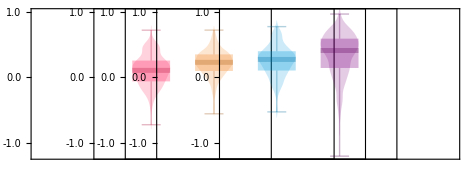

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,v2mAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```